# L5PN Ca data fitting with SiCoMo and kappa

Concentrations in mol/l
Includes Ca indicator dye and assumptions about slow and fast endogenous buffers and ATP
Loads imaging data
Updates: Dec. 2017: Inclusion of L-type channels, 2APs added
Jan. 2018: Multiple APs; data scaling

## General Parameters

```mathematica
TimeWindow=0.15;

APN=1;
ISI=20.*10^-3;


Vb=0.127*10^-15;  (*Schikorski & Stevens, PNAS, 1999; olfactory cortex; corrected for space occupied by vesicles and organelles, factor 0.635 (Wilhelm et al., Science, 2014): 0.2 * 0.635*)

F=9.65*10^4;
NA=6.022*10^23;
ECa=130.*10^-3;
Vrest=-80.*10^-3;
CaRest=37.*10^-9;

(*Buffer capacity; used to calculate concentrations of unknown edogenous buffers*)
```

## Influx

### Action potential and Ca channels

#### APs: Unitstep with Double Exp Function

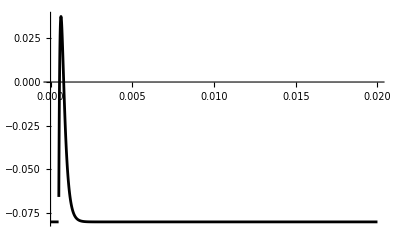

```mathematica
Clear[Vm,startT,taud,taur]
startT=0.5*10^-3;
taud=0.2*10^-3;
taur=0.1*10^-3;

Vm=Sum[(UnitStep[t-i]*(Exp[-(t-i)/taud]-Exp[-(t-i)/taur])),{i,startT,startT+(APN-1)*ISI,ISI}];
Vm=0.47*Vm-0.08;
plAP=Plot[Vm,{t,0,APN*ISI},PlotRange->All,PlotStyle->Black]
```

#### P/Q type channel

(Li et al., J Neurosci, 2007; cf. Ermolyuk et al., Nat Neurosci, 2013 and Scimemi et al., J Neurosci, 2012)

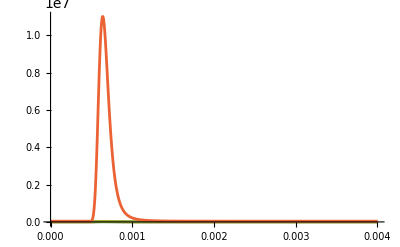

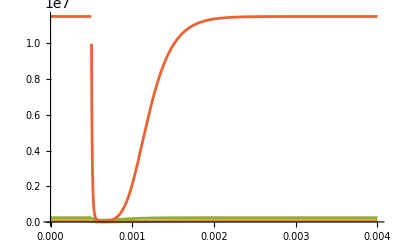

```mathematica
Clear[α,Α,β,Β]

gPQ=2.5*10^-12;   (*assumed values as in the above papers*)

α[1]=5.89*10^3;
α[2]=9.21*10^3;
α[3]=5.2*10^3;
α[4]=1823.18*10^3;
Α=247.71*10^3;

β[1]=14.99*10^3;
β[2]=6.63*10^3;
β[3]=132.8*10^3;
β[4]=248.58*10^3;
Β=8.28*10^3;

k[1]=62.61*10^-3;
k[2]=33.92*10^-3;
k[3]=135.08*10^-3;
k[4]=20.86*10^-3;

Table[alpha[i]=α[i] Exp[Vm/k[i]],{i,1,4}];
Table[beta[i]=β[i] Exp[-Vm/k[i]],{i,1,4}];

Plot[{alpha[1],alpha[2],alpha[3],alpha[4]},{t,0,0.004},PlotRange->All]
Plot[{beta[1],beta[2],beta[3],beta[4]},{t,0,0.004},PlotRange->All]
```

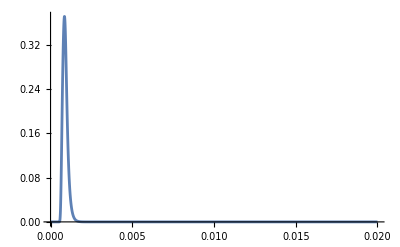

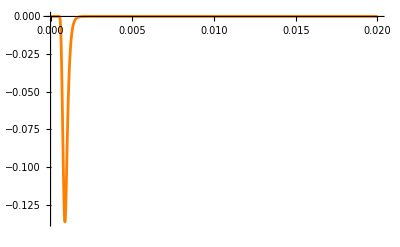

```mathematica
PQChannel={
PQCh0[0]==1,
PQCh1[0]==0,
PQCh2[0]==0,
PQCh3[0]==0,
PQCh4[0]==0,
PQChOpen[0]==0,

PQCh0'[t]==-PQCh0[t]*alpha[1]+PQCh1[t]*beta[1],

PQCh1'[t]==-PQCh0'[t]-PQCh1[t]*alpha[2]+PQCh2[t]*beta[2],

PQCh2'[t]==PQCh1[t]*alpha[2]-PQCh2[t]*beta[2]-PQCh2[t]*alpha[3]+PQCh3[t]*beta[3],

PQCh3'[t]==PQCh2[t]*alpha[3]-PQCh3[t]*beta[3]-PQCh3[t]*alpha[4]+PQCh4[t]*beta[4],

PQCh4'[t]==PQCh3[t]*alpha[4]-PQCh4[t]*beta[4]-PQCh4[t]*Α+PQChOpen[t]*Β,

PQChOpen'[t]==PQCh4[t]*Α-PQChOpen[t]*Β};



VarsPQ={PQCh0,PQCh1,PQCh2,PQCh3,PQCh4,PQChOpen};

sol:=NDSolve[PQChannel,VarsPQ,{t,0,TimeWindow},MaxStepSize->0.001]

Plot[Evaluate[{PQChOpen[t]}/.sol],{t,0,APN*ISI},PlotRange->All]

plPQ=Plot[Evaluate[10^12*gPQ*(Vm-ECa)*PQChOpen[t]/.sol],{t,0,APN*ISI},PlotRange->All,PlotStyle->Orange]
```

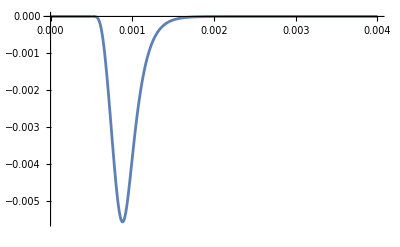

{{1.97752×10^-6}}

{{151.24}}

```mathematica
InfluxPQ:=(1/(2 F Vb))*gPQ*(Vm-ECa)*PQChOpen[t]
InPQ:=Evaluate[(1/(2 F Vb))*gPQ*(Vm-ECa)*{PQChOpen[t]}/.sol]
Plot[InPQ,{t,0,0.004},PlotRange->All]
conc=NIntegrate[-InPQ,{t,0,0.004}]
CaIons=conc*NA*Vb
```

#### N type channel

(Li et al., J Neurosci, 2007; cf. Ermolyuk et al., Nat Neurosci, 2013 and Scimemi et al., J Neurosci, 2012)

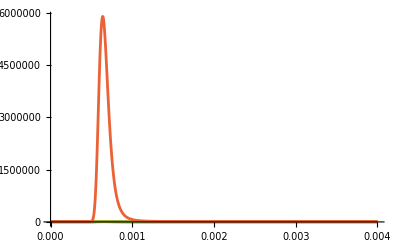

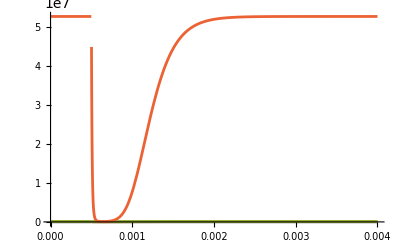

```mathematica
Clear[αN,ΑN,βN,ΒN]

gN=2.5*10^-12;

αN[1]=4.29*10^3;
αN[2]=5.24*10^3;
αN[3]=4.98*10^3;
αN[4]=772.63*10^3;
ΑN=615.01*10^3;

βN[1]=5.23*10^3;
βN[2]=6.63*10^3;
βN[3]=73.89*10^3;
βN[4]=692.18*10^3;
ΒN=7.68*10^3;

kN[1]=68.75*10^-3;
kN[2]=39.53*10^-3;
kN[3]=281.62*10^-3;
kN[4]=18.46*10^-3;

Table[alphaN[i]=αN[i] Exp[Vm/kN[i]],{i,1,4}];
Table[betaN[i]=βN[i] Exp[-Vm/kN[i]],{i,1,4}];

Plot[{alphaN[1],alphaN[2],alphaN[3],alphaN[4]},{t,0,0.004},PlotRange->All]
Plot[{betaN[1],betaN[2],betaN[3],betaN[4]},{t,0,0.004},PlotRange->All]
```

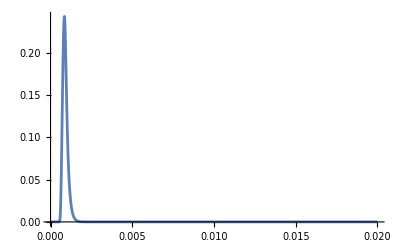

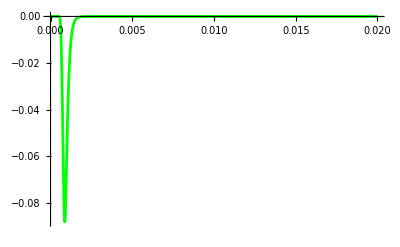

```mathematica
NChannel={
NCh0[0]==1,
NCh1[0]==0,
NCh2[0]==0,
NCh3[0]==0,
NCh4[0]==0,
NChOpen[0]==0,

NCh0'[t]==-NCh0[t]*alphaN[1]+NCh1[t]*betaN[1],

NCh1'[t]==-NCh0'[t]-NCh1[t]*alphaN[2]+NCh2[t]*betaN[2],

NCh2'[t]==NCh1[t]*alphaN[2]-NCh2[t]*betaN[2]-NCh2[t]*alphaN[3]+NCh3[t]*betaN[3],

NCh3'[t]==NCh2[t]*alphaN[3]-NCh3[t]*betaN[3]-NCh3[t]*alphaN[4]+NCh4[t]*betaN[4],

NCh4'[t]==NCh3[t]*alphaN[4]-NCh4[t]*betaN[4]-NCh4[t]*ΑN+NChOpen[t]*ΒN,

NChOpen'[t]==NCh4[t]*ΑN-NChOpen[t]*ΒN};



VarsN:={NCh0,NCh1,NCh2,NCh3,NCh4,NChOpen}

solN:=NDSolve[NChannel,VarsN,{t,0,TimeWindow},MaxStepSize->0.001]

Plot[Evaluate[{NChOpen[t]}/.solN],{t,0,APN*ISI},PlotRange->All]

plN=Plot[Evaluate[10^12*gN*(Vm-ECa)*{NChOpen[t]}/.solN],{t,0,APN*ISI},PlotRange->{0,-0.15},PlotStyle->Green]
```

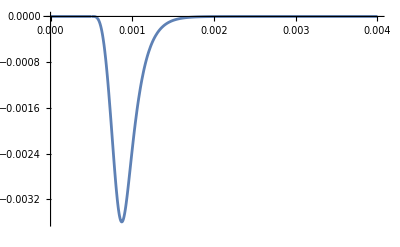

{{1.24531×10^-6}}

{{95.2407}}

```mathematica
InfluxN:=(1/(2 F Vb))*gN*(Vm-ECa)*NChOpen[t]
InN:=Evaluate[(1/(2 F Vb))*gN*(Vm-ECa)*{NChOpen[t]}/.solN]
Plot[InN,{t,0,0.004},PlotRange->All]
concN=NIntegrate[-InN,{t,0,0.004}]
CaIonsN=concN*NA*Vb
```

#### R type channel

(Li et al., J Neurosci, 2007; cf. Ermolyuk et al., Nat Neurosci, 2013 and Scimemi et al., J Neurosci, 2012)

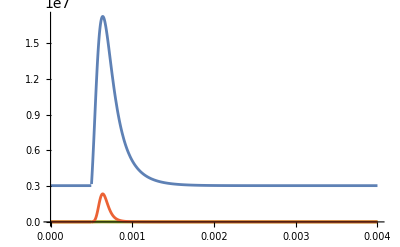

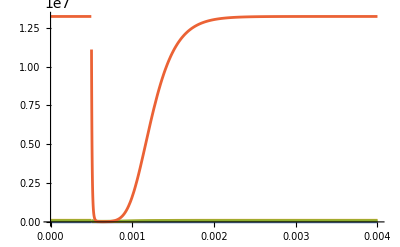

```mathematica
Clear[αR,ΑR,βR,ΒR]

gR=2.5*10^-12;

αR[1]=9911.36*10^3;
αR[2]=4.88*10^3;
αR[3]=4*10^3;
αR[4]=256.41*10^3;
ΑR=228.83*10^3;

βR[1]=0.62*10^3;
βR[2]=21.91*10^3;
βR[3]=51.3*10^3;
βR[4]=116.97*10^3;
ΒR=1.78*10^3;

kR[1]=67.75*10^-3;
kR[2]=50.94*10^-3;
kR[3]=173.29*10^-3;
kR[4]=16.92*10^-3;

Table[alphaR[i]=αR[i] Exp[Vm/kR[i]],{i,1,4}];
Table[betaR[i]=βR[i] Exp[-Vm/kR[i]],{i,1,4}];

Plot[{alphaR[1],alphaR[2],alphaR[3],alphaR[4]},{t,0,0.004},PlotRange->All]
Plot[{betaR[1],betaR[2],betaR[3],betaR[4]},{t,0,0.004},PlotRange->All]
```

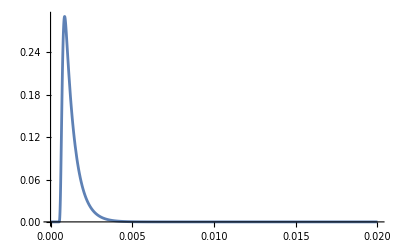

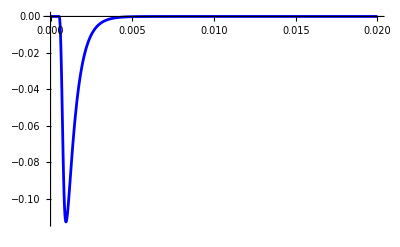

```mathematica
RChannel={
RCh0[0]==1,
RCh1[0]==0,
RCh2[0]==0,
RCh3[0]==0,
RCh4[0]==0,
RChOpen[0]==0,

RCh0'[t]==-RCh0[t]*alphaR[1]+RCh1[t]*betaR[1],

RCh1'[t]==-RCh0'[t]-RCh1[t]*alphaR[2]+RCh2[t]*betaR[2],

RCh2'[t]==RCh1[t]*alphaR[2]-RCh2[t]*betaR[2]-RCh2[t]*alphaR[3]+RCh3[t]*betaR[3],

RCh3'[t]==RCh2[t]*alphaR[3]-RCh3[t]*betaR[3]-RCh3[t]*alphaR[4]+RCh4[t]*betaR[4],

RCh4'[t]==RCh3[t]*alphaR[4]-RCh4[t]*betaR[4]-RCh4[t]*ΑR+RChOpen[t]*ΒR,

RChOpen'[t]==RCh4[t]*ΑR-RChOpen[t]*ΒR};



VarsR:={RCh0,RCh1,RCh2,RCh3,RCh4,RChOpen}

solR:=NDSolve[RChannel,VarsR,{t,0,TimeWindow},MaxStepSize->0.001]

Plot[Evaluate[{RChOpen[t]}/.solR],{t,0,APN*ISI},PlotRange->All]

plR=Plot[Evaluate[10^12*gR(Vm-ECa)*{RChOpen[t]}/.solR],{t,0,APN*ISI},PlotRange->{0,-0.15},PlotStyle->Blue]
```

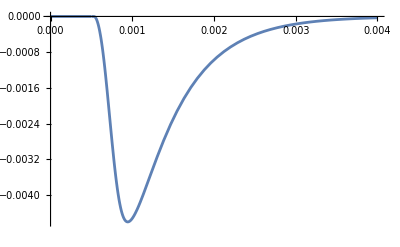

{{4.27816×10^-6}}

{{327.191}}

```mathematica
InfluxR:=(1/(2 F Vb))*gR*(Vm-ECa)*RChOpen[t]
InR:=Evaluate[(1/(2 F Vb))*gR*(Vm-ECa)*{RChOpen[t]}/.solR]
Plot[InR,{t,0,0.004},PlotRange->All]
concR=NIntegrate[-InR,{t,0,0.004}]
CaIonsR=concR*NA*Vb
```

#### L type channel simple

(Beyl et al., J Gen Physiol, 2009)

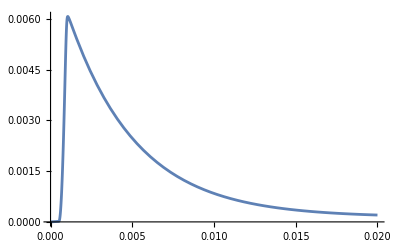

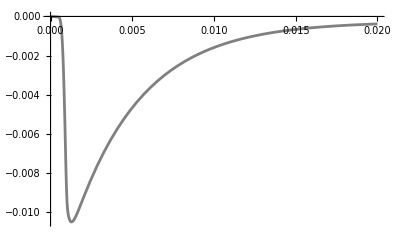

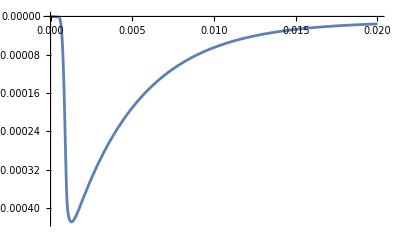

{{2.18408×10^-6}}

{{167.037}}

```mathematica
Clear[αL,ΑL,βL,ΒL]

gL=9*10^-12;   (*von Wegner & Fink, Eur Biophys J, 2010.*)

αL=0.427*10^3;
ΑL=0.15*10^3;

βL=0.216*10^3;
ΒL=0.24*10^3;

kLa=328.8*10^-3;
kLb=9.04*10^-3;

alphaL=αL Exp[Vm/kLa];
betaL=βL Exp[-Vm/kLb];

LChannel={
LCh0[0]==1,
LCh1[0]==0,
LChOpen[0]==0,

LCh0'[t]==-LCh0[t]*alphaL+LCh1[t]*betaL,

LCh1'[t]==-LCh0'[t]-LCh1[t]*ΑL+LChOpen[t]*ΒL,

LChOpen'[t]==LCh1[t]*ΑL-LChOpen[t]*ΒL};


VarsL:={LCh0,LCh1,LChOpen}

solL:=NDSolve[LChannel,VarsL,{t,0,TimeWindow},MaxStepSize->0.001]

Plot[Evaluate[{LChOpen[t]}/.solL],{t,0,APN*ISI},PlotRange->All]

plL=Plot[Evaluate[10^12*gL(Vm-ECa)*{LChOpen[t]}/.solL],{t,0,APN*ISI},PlotRange->{0,-0.15},PlotStyle->Gray]

InfluxL:=(1/(2 F Vb))*gL*(Vm-ECa)*LChOpen[t]
InL:=Evaluate[(1/(2 F Vb))*gL*(Vm-ECa)*{LChOpen[t]}/.solL]
Plot[InL,{t,0,0.02},PlotRange->All]
concL=NIntegrate[-InL,{t,0,0.02}]
CaIonsL=concL*NA*Vb
```

#### Or: L type channel simple with deactivation

(Beyl et al., J Gen Physiol, 2009)

```mathematica
(*Clear[αL,ΑL,βL,ΒL]

gL=24*10^-12;      (*Weber et al., Nat Neurosci, 2010*)

αL=0.427*10^3;      (*x0 in Beyl et al.*)
ΑL=0.15*10^3;      (*α in Beyl et al.*)


βL=0.216*10^3;    (*y0 in Beyl et al.*)
ΒL=0.24*10^3;     (*β in Beyl et al.*)

δ=1.39*10^3;
γ=0.021*10^3;

kLa=328.8*10^-3;      (*kx in Beyl et al.*)
kLb=9.04*10^-3;      (*ky in Beyl et al.*)

u0=αL*δ/γ;
w0=βL*ΒL/ΑL;

alphaL=αL Exp[Vm/kLa];      (*x(V) in Beyl et al.*)
betaL=βL Exp[-Vm/kLb];      (*y(V) in Beyl et al.*)
uL=u0 Exp[Vm/kLa];
wL=w0 Exp[-Vm/kLb];




LChannel={
LCh0[0]==1,
LCh1[0]==0,
LChOpen[0]==0,
LChD[0]==0,

LCh0'[t]==-LCh0[t]*alphaL+LCh1[t]*betaL+LChD[t]*δ(*-LCh0[t]*γ*),

LCh1'[t]==+LCh0[t]*alphaL-LCh1[t]*betaL-LCh1[t]*ΑL+LChOpen[t]*ΒL,

LChOpen'[t]==LCh1[t]*ΑL-LChOpen[t]*ΒL-LChOpen[t]*wL+LChD[t]*uL,

LChD'[t]==LChOpen[t]*wL-LChD[t]*uL-LChD[t]*δ(*+LCh0[t]*γ*)};


VarsL:={LCh0,LCh1,LChOpen,LChD}

solL:=NDSolve[LChannel,VarsL,{t,0,TimeWindow},MaxStepSize->0.001]


Plot[Evaluate[{LChOpen[t]}/.solL],{t,0,0.004},PlotRange->All]

plL1=Plot[Evaluate[10^12*gL(Vm-ECa)*{LChOpen[t]}/.solL],{t,0,0.004},PlotRange->All,PlotStyle->LightGray]
InfluxL:=(1/(2 F Vb))*gL*(Vm-ECa)*LChOpen[t]
InL:=Evaluate[(1/(2 F Vb))*gL*(Vm-ECa)*{LChOpen[t]}/.solL]
Plot[InL,{t,0,0.004},PlotRange->All]
concL=NIntegrate[-InL,{t,0,0.004}]
CaIonsL=concL*NA*Vb*)
```

#### Or: L type channel simple 2

(von Wegner & Fink, Eur Biophys J, 2010)

```mathematica
(*Clear[VarsL,LChannel,solL]
gL=24*10^-12;
V0=0.035;

f=0.85*10.^3;
g=2*10.^3;
α0L=2*10.^3;
α1L=0.012*10.^3;
β0L=0.0882*10.^3;
β1L=-0.05*10^3;

αL=α0L*Exp[α1L*(Vm-V0)];
βL=β0L*Exp[β1L*(Vm-V0)];

Plot[{αL},{t,0,0.004},PlotRange->All]
Plot[{βL},{t,0,0.004},PlotRange->All]

LChannel={
C0[0]==1,
C1[0]==0,
C2[0]==0,
C3[0]==0,
C4[0]==0,
LO[0]==0,

C0'[t]==-4* αL* C0[t]+βL *C1[t],
C1'[t]==4* αL *C0[t]-βL* C1[t]-3* αL* C1[t]+2* βL* C2[t],
C2'[t]==3* αL *C1[t]-2* βL *C2[t]-2 *αL* C2[t]+3* βL* C3[t],
C3'[t]==2 *αL* C2[t]-3* βL* C3[t]-αL* C3[t]+4 *βL* C4[t],
C4'[t]== αL* C3[t]-4* βL *C4[t]-f* C4[t]+g* LO[t],
LO'[t]== f* C4[t]-g* LO[t]
};


VarsL={C0,C1,C2,C3,C4,LO};


solL:=NDSolve[LChannel,VarsL,{t,0,TimeWindow}]

IL=10^12*gL*LO[t]*(Vm-ECa);
InfluxL:=(1/(2 F Vb))*gL*(Vm-ECa)*LO[t]
InL:=Evaluate[(1/(2 F Vb))*gL*(Vm-ECa)*{LO[t]}/.solL]
Plot[InL,{t,0,0.004},PlotRange->All]
concL=NIntegrate[-InL,{t,0,0.004}]
CaIonsL=concL*NA*Vb

plL2=Plot[Evaluate[IL/.solL],{t,0,0.004},PlotRange->All]*)
```

#### Showing

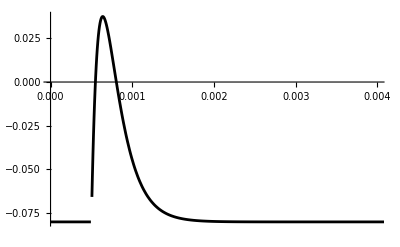

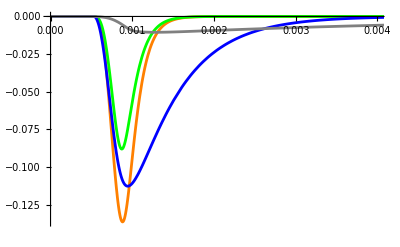

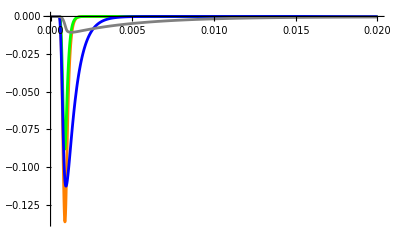

```mathematica
Show[{plAP},PlotRange->{{0,0.004},All}]
Show[plPQ,plN,plR,plL,PlotRange->{{0,0.004},All}]
Show[plPQ,plN,plR,plL,PlotRange->{{0,APN*ISI},All}]
```

## Calcium

#### Parameters

```mathematica
CaFrac=1;     (*According to Ca imaging toxin data scaled to 100%: AgTx, 0.36; AgTX+CTx, 0.26*)
(*kappa 120*)
(*NPQ=12; (*10-11*)
NN=4;  (*2-3*)
NR=2;  (*1-2*)
γ=3200.;*)

(*kappa 25*)
NPQ=33; (*10-11*)
NN=0;  (*2-3*)
NR=0;  (*1-2*)
γ=3000.; 

NL=0;   
(*γ=3200.;   *)              (*fit parameter; 2600 in Koester & Sakmann, J Physiol, 2000 for L2/3*)
```

#### Calcium with kappa (Helmchen & Tank, Single compartment model)

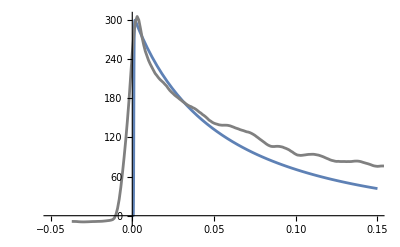

```mathematica
Clear[κB]

(*κS=120.;*)              (*105-135; Helmchen et al., Biophys J, 1996; no substantial mobility or wash-out;  140 for L2/3 in Koester & Sakmann, J Physiol, 2000; kappa fix =100 in CA1, Matthews et al., J Neurosci, 2013 but not in Pyramids*)

κS=25.; (*Tran & Stricker, Biophys J, 2018; L5PN boutons; kappa 7 or 25; no mobile buffers*)

OGtotal=140.*10^-6;
KdOG=0.439*10^-6;

κB=(OGtotal*KdOG)/(Ca[t]+KdOG)^2;
(*κB=(OGtotal*KdOG)/(CaRest+KdOG)^2;*)
(*κB=OGtotal/(KdOG);*)


CaRest=0;
FreeCa:= {
Ca[0]==CaRest,

Ca'[t]== (NPQ*(-InfluxPQ)+NN*(-InfluxN)+NR*(-InfluxR)+NL*(-InfluxL)-γ (Ca[t]-CaRest))/(1+κB+κS)
}

Eqns:={FreeCa,PQChannel,NChannel,RChannel,LChannel}
Vars:={Ca,VarsPQ,VarsN,VarsR,VarsL}
sol1 := NDSolve[Eqns,Vars,{t,0.,TimeWindow},MaxStepSize->0.001]

SetDirectory["/Users/hartmutschmidt/Documents/Cortical coupling distance map/Mathematica"];
(*DataAdult=Import["AgaConoSensitive.txt","Table"];
DataAdult1=Import["Avg_aga_cono_sensitive.txt","Table"];*)
DataControl=Import["Ca_PFC.txt","Table"];

n=Length[DataControl];
Sub=Table[{0.037,38.},n];
d1=DataControl-Sub;
Mult=Table[{1,CaFrac},n];
dscale=d1*Mult;


pl1:=Plot[Evaluate[{10^9*Ca[t]}/.sol1],{t,0,TimeWindow},PlotRange->All]
pl2:=ListPlot[dscale,PlotRange->All,PlotStyle->Gray,Joined->True]
pl3:=ListPlot[(DataControl-0.055),PlotRange->All,PlotStyle->Gray]

Show[pl1,pl2, PlotRange->{{-0.05,TimeWindow},All}]
```